# on-chip MBQC machines of NV-center

## VQD setup

Set the main directory as the current directory

```mathematica
SetDirectory[NotebookDirectory[]];
```

Load the QuESTLink package
One may also use the off-line questlink.m file, change it to the location of the local file

```mathematica
Quiet@Import["https://qtechtheory.org/questlink.m"]
```

This will download a binary file  quest_link from the repo; some error will show if the system tries to override the file

Use CreateLocalQuESTEnv[quest_link_file] to use the existing binary

```mathematica
(*CreateDownloadedQuESTEnv[];*)
CreateLocalQuESTEnv["quest_link"]
```

LinkObject[…]

Load the VQD package; must be loaded after QuESTlink is loaded

```mathematica
Import["https://raw.githubusercontent.com/QTechTheory/VQD/refs/heads/master/vqd.wl"]
```

## Native gates

Direct iIitialisation and measurement are on the NV electron spin only
Init_0, M_0
Single-qubit gates
Rx_q[θ], Ry_q[θ], Rz_q[θ] 
Two-qubit gates are conditional rotation, where  CRσ[θ]:=|0X0|⊗ Rσ[θ]+|1X1|⊗ Rσ[-θ]
CRx_(0,q)[θ], CRy_(0,q)[θ]
others: doing nothing
Wait_q[duration]

## User device configuration

Qubit 0 indicates electron spin,and the rest are nuclear spins  C^13 and N^14 - if applicable
Time unit is second (s)
Frequency unit is  Hertz (Hz)

In the following example, we have a 4-qubit system. Q0 -> Electronic spin qubit and the rest are Nuclear spin qubits

```mathematica
Options[NVCenterDelft]={
QubitNum->4,
(* T1 of each qubit *)
T1-> <|0-> 3600,1->60,2->60,3->60 |>,
(* T2 of each qubit; we assume dynamical decoupling is actively applied *)
T2-> <|0-> 1.5,1->10,2->10,3->10|>,
(* dipolar interaction among nuclear spins: cross-talk ZZ-coupling in order of a few Hz on passive noise *)
FreqWeakZZ->5,
(* direct single rotation on Nuclear spin is done via RF, put electron in state -1 leave out the Rx Ry on nuclear spins ideally. *)
FreqSingleXY-> <|0->15*10^6,1->500 ,2->500,3->500|>,
(* usually done virtually *)
FreqSingleZ-><|0->32*10^6,1->400*10^3,2->400*10^3,3->400*10^3|>,
(* Frequency of CRot gate, conditional rotation done via dynamical decoupling or dd+RF. The gate is conditioned on electron spin state *)
FreqCRot-> <|1-> 1.5*10^3,2->2.8*10^3,3->0.8*10^3|>,
(* Fidelity of CRot gate  *)
FidCRot-><|1-> 0.98,2->0.98, 3->0.98|>,
(* fidelity of x- and y- rotations on each qubit *)
FidSingleXY-> <| 0->0.9995,1-> 0.995,2->0.995, 3->0.99|>,
(* fidelity of z- rotations on each qubit *)
FidSingleZ->  <| 0->0.9999,1-> 0.9999,2->0.99999, 3->0.9999 |>,
(* Error ratio of 1-qubit depolarising:dephasing of x- and y- rotations  *)
EFSingleXY->{0.75,0.25},
(* Error ratio of 2-qubit depolarising:dephasing of CRot gate *)
EFCRot->{0.9,0.1},
(* initialization fidelity on the electron spin *)
FidInit-> 0.999,
(* initialization duration on the electron spin *)
DurInit->2*10^-3,
(* measurement fidelity on the electron spin *)
FidMeas->0.946,
(* measurement duration on the electron spin *)
DurMeas->2*10^-5
};
```

-Graphics-

```mathematica
(* Create an NV-center instance *)
NVDevice=NVCenterDelft[];
```

## QuESTlink and convention

QuEST uses Least Significant Bit
QuEST uses Superopeator to store and perform operation on density matrices

By LSB, therefore:
Column-stacking:  A_(i,j)|i X j| :> A_(i,j)j i : { 00, 10, 01, (11})_(q0, q1),  in QuEST: {00,01,10,11}_(q1,q0)
Row-stacking: A_(i,j)|i X j| :> A_(i,j)i j: {00, 01, 10, (11})_(q0,q1), in QuEST: {00,10,01,11}_(q1,q0)

```mathematica
Stacking::usage="Pick row or colum stacking. By default, it's row stacking";
Options[Vectorize] = {Stacking -> "row"};
Vectorize[m_, OptionsPattern[]] := ArrayReshape[
	If[OptionValue[Stacking] == "row",
		TensorTranspose[m , {2, 1}],
	m]
,
 {Times @@ Dimensions @ m}]
 
 Options[Tensorize] = {Stacking -> "row"};
 Tensorize::usage = "Turns a vector into 2x2 matrix. By default, it's row stacking";
 Tensorize[v_, OptionsPattern[]] := With[ {d = Round @ Sqrt @ First @ Times @ Dimensions @ v},
 If[ OptionValue @ Stacking === "row", 
 TensorTranspose[ArrayReshape[v, {d, d}], {2, 1}]
 ,
 ArrayReshape[v, {d, d}]
 ]
 ]
 
SuperOperate::usage="SuperOperate[ρmatrix, superoperator]";
SuperOperate[ρmat_, superop_]:=Tensorize[superop.Vectorize[ρmat]]
```

## Preparation operation

XY-plane basis: +_θ= {1/(√2),ⅇ^(ⅈ θ)/(√2)} and -_θ={1/(√2),-ⅇ^(ⅈ θ)/(√2)}
 Note that, NV center has star connectivity . Initialisation of the qubit happens on the center qubit (electron spin qubit) . See “Native Gates” section
 My strategy here is prepare the state in the center, then perform partial SWAP to the edge qubits (Nuclear spin qubits).
 Here we do not need the full swap because the states are rebits (Real qubits)

```mathematica
xyDensityMatrix::usage="xyDensityMatrix[θ]. Create rebit in XY plane with parameter θ";
xyDensityMatrix[θ_]:=KroneckerProduct[{1/(√2),ⅇ^(ⅈ θ)/(√2)},{1/(√2),ⅇ^(-ⅈ θ)/(√2)}]
```

In vector simulation, the state can be obtained by two single rotations. The following operations show the ideal case should be able to prepare any XY-state
This direct operation can be done on the electronic spin

```mathematica
mat = CalcCircuitMatrix[{Subscript[Ry, 0][π/2],Subscript[Rz, 0][θ]}]
```

{{ⅇ^(-(ⅈ θ)/2)/(√2),-ⅇ^(-(ⅈ θ)/2)/(√2)},{ⅇ^((ⅈ θ)/2)/(√2),ⅇ^((ⅈ θ)/2)/(√2)}}

```mathematica
(* State +θ*)
ⅇ^(ⅈ θ/2)*mat.{1,0}
```

{1/(√2),ⅇ^(ⅈ θ)/(√2)}

```mathematica
(* State -θ*)
-ⅇ^(ⅈ θ/2)*mat.{0,1}
```

{1/(√2),-ⅇ^(ⅈ θ)/(√2)}

### Prepare XY - state on the electron spin

```mathematica
xyElectron[θ_]:=Sequence@@{Subscript[Init, 0],Subscript[Ry, 0][π/2],Subscript[Rz, 0][θ]}
```

```mathematica
Flatten[{xyElectron[θ]}/.NVDevice[Aliases]]
supop1=CalcCircuitMatrix@%
```

{Damp_0[1.],Ry_0[π/2],Rz_0[θ]}

{{0.5,0.,0.,0.5},{0.+0.5 ⅇ^(ⅈ θ),0.,0.,0.+0.5 ⅇ^(ⅈ θ)},{0.+0.5 ⅇ^(-ⅈ θ),0.,0.,0.+0.5 ⅇ^(-ⅈ θ)},{0.5,0.,0.,0.5}}

Density matrix test: Start with an arbirary random mix density matrix  and see if the electron spin is initialised to the XY-plane states

```mathematica
ρmat1=RandomMixState@1
```

{{0.192532,-0.272511-0.123977 ⅈ},{-0.272511+0.123977 ⅈ,0.807468}}

```mathematica
(* Superoperate *)
Chop@SuperOperate[ρmat1, supop1]
(* compare to the GOAL*)
xyDensityMatrix@θ
```

{{0.5,0.5 ⅇ^(-ⅈ θ)},{0.5 ⅇ^(ⅈ θ),0.5}}

{{1/2,ⅇ^(-ⅈ θ)/2},{ⅇ^(ⅈ θ)/2,1/2}}

### Prepare XY - state on the nuclear spin

```mathematica
Subscript[xyNuclear, q_/;q>0][θ_]:=Sequence@@{Subscript[Init, 0],Subscript[Ry, 0][π/2],Subscript[CRx, 0,q][π/2],Subscript[Rx, 0][π/2],Subscript[CRy, 0,q][-π/2],Subscript[Ry, q][π/2],Subscript[Rz, q][θ]}
```

```mathematica
Flatten[{Subscript[xyNuclear, 1][θ]}/.NVDevice[Aliases]]
supop2=CalcCircuitMatrix@%;
```

{Damp_0[1.],Ry_0[π/2],U_(0,1)[{{1/(√2),0,-ⅈ/(√2),0},{0,1/(√2),0,ⅈ/(√2)},{-ⅈ/(√2),0,1/(√2),0},{0,ⅈ/(√2),0,1/(√2)}}],Rx_0[π/2],U_(0,1)[{{1/(√2),0,1/(√2),0},{0,1/(√2),0,-1/(√2)},{-1/(√2),0,1/(√2),0},{0,1/(√2),0,1/(√2)}}],Ry_1[π/2],Rz_1[θ]}

Density matrix test: Start with an arbirary random mix density matrix  and see if the nuclear spin is initialised to the XY-plane states

```mathematica
ρmat2=RandomMixState@2
```

{{0.247792,0.00873419-0.0685634 ⅈ,-0.203223-0.101719 ⅈ,-0.00228545+0.123116 ⅈ},{0.00873419+0.0685634 ⅈ,0.173088,0.0509583-0.0314637 ⅈ,0.0329066+0.0133302 ⅈ},{-0.203223+0.101719 ⅈ,0.0509583+0.0314637 ⅈ,0.445735,0.0434399-0.120506 ⅈ},{-0.00228545-0.123116 ⅈ,0.0329066-0.0133302 ⅈ,0.0434399+0.120506 ⅈ,0.133384}}

```mathematica
(* Superoperate, then trace the electron spin *)
PartialTrace[Chop@SuperOperate[ρmat2, supop2],0]
(* compare to the GOAL*)
xyDensityMatrix@θ
```

{{0.5,0.5 ⅇ^(-ⅈ θ)},{0.5 ⅇ^(ⅈ θ),0.5}}

{{1/2,ⅇ^(-ⅈ θ)/2},{ⅇ^(ⅈ θ)/2,1/2}}

## NOISY preparation on 4-qubit NV-center

Questions : Should I give out the explicit superoperator for each θ?

Noisy preparing the electron spin to state +θ

```mathematica
elprep={xyElectron[θ]}
```

{Init_0,Ry_0[π/2],Rz_0[θ]}

```mathematica
elprepNoisy=Assuming[Element[θ,Reals],Simplify@InsertCircuitNoise[elprep,NVDevice,ReplaceAliases->True]]
```

{{0,{Damp_0[0.999]},{Depol_0[0.],Deph_0[0.],R[0,Z_1 Z_2],R[0,Z_1 Z_3],R[0,Z_2 Z_3],Depol_1[0.0000249996],Deph_1[0.00009999],R[1/2500,Z_2 Z_3],Depol_2[0.0000249996],Deph_2[0.00009999],R[1/2500,Z_1 Z_3],Depol_3[0.0000249996],Deph_3[0.00009999],R[1/2500,Z_1 Z_2]}},{1/500,{Ry_0[π/2],Depol_0[0.000281303],Deph_0[0.0000937676]},{Depol_0[0.],Deph_0[0.],R[0,Z_1 Z_2],R[0,Z_1 Z_3],R[0,Z_2 Z_3],Depol_1[1.309×10^-9],Deph_1[5.23599×10^-9],R[π/150000000,Z_2 Z_3],Depol_2[1.309×10^-9],Deph_2[5.23599×10^-9],R[π/150000000,Z_1 Z_3],Depol_3[1.309×10^-9],Deph_3[5.23599×10^-9],R[π/150000000,Z_1 Z_2]}},{(60000+π)/30000000,{Rz_0[θ],Deph_0[Min[0.5,0.0000477465 Abs[θ]]]},{Depol_0[0.],Deph_0[0.],R[0,Z_1 Z_2],R[0,Z_1 Z_3],R[0,Z_2 Z_3],Depol_1[0.75-0.75 ⅇ^(-Abs[θ]/1920000000)],Deph_1[0.5-0.5 ⅇ^(-Abs[θ]/320000000)],R[Abs[θ]/160000000,Z_2 Z_3],Depol_2[0.75-0.75 ⅇ^(-Abs[θ]/1920000000)],Deph_2[0.5-0.5 ⅇ^(-Abs[θ]/320000000)],R[Abs[θ]/160000000,Z_1 Z_3],Depol_3[0.75-0.75 ⅇ^(-Abs[θ]/1920000000)],Deph_3[0.5-0.5 ⅇ^(-Abs[θ]/320000000)],R[Abs[θ]/160000000,Z_1 Z_2]}},{(16 (60000+π)+15 Abs[θ])/480000000,{},{}}}

Note that here is only preparing the electronic spin state to XY plane. Notice the presence of Cross-talk are forming all-to-all connectivity

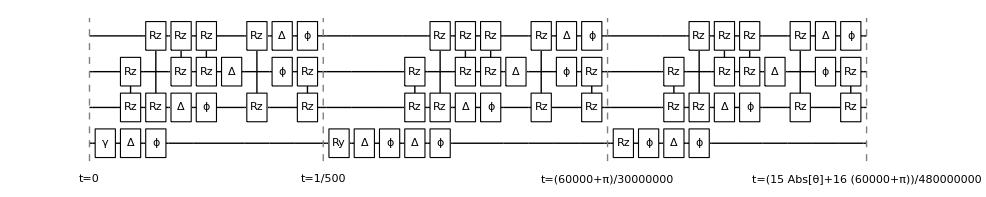

```mathematica
DrawCircuit[elprepNoisy]
```

Try all states from the same random density matrix

```mathematica
DestroyAllQuregs[]
```

```mathematica
ρ4=CreateDensityQureg[4]
```

0

```mathematica
ρinit=RandomMixState@4;
TableForm@Table[
param=j π/4;
noisycirc=ExtractCircuit[ elprepNoisy/.θ->param];
(* cross check, if superoperate operates the same way as QuEST*)
SetQuregMatrix[ρ4,ρinit];
ApplyCircuit[ρ4,noisycirc];
ρetom=PartialTrace[GetQuregState@ρ4,1,2,3];
ρeid=xyDensityMatrix[param];
{param, CalcFidelityDensityMatrices[ρetom,ρeid],MatrixForm@Chop@ρetom, MatrixForm@Chop@N@ρeid}
,{j,0,7}]
```

0 | 0.999202 | (0.50184 | 0.499202+0.000752607 ⅈ
0.499202-0.000752607 ⅈ | 0.49816) | (0.5 | 0.5
0.5 | 0.5)
π/4 | 0.999164 | (0.50184 | 0.353495-0.35243 ⅈ
0.353495+0.35243 ⅈ | 0.49816) | (0.5 | 0.353553-0.353553 ⅈ
0.353553+0.353553 ⅈ | 0.5)
π/2 | 0.999127 | (0.50184 | 0.000752494-0.499127 ⅈ
0.000752494+0.499127 ⅈ | 0.49816) | (0.5 | 0.-0.5 ⅈ
0.+0.5 ⅈ | 0.5)
(3 π)/4 | 0.999089 | (0.50184 | -0.352377-0.353442 ⅈ
-0.352377+0.353442 ⅈ | 0.49816) | (0.5 | -0.353553-0.353553 ⅈ
-0.353553+0.353553 ⅈ | 0.5)
π | 0.999052 | (0.50184 | -0.499052-0.000752381 ⅈ
-0.499052+0.000752381 ⅈ | 0.49816) | (0.5 | -0.5
-0.5 | 0.5)
(5 π)/4 | 0.999015 | (0.50184 | -0.353389+0.352325 ⅈ
-0.353389-0.352325 ⅈ | 0.49816) | (0.5 | -0.353553+0.353553 ⅈ
-0.353553-0.353553 ⅈ | 0.5)
(3 π)/2 | 0.998977 | (0.50184 | -0.000752268+0.498977 ⅈ
-0.000752268-0.498977 ⅈ | 0.49816) | (0.5 | 0.+0.5 ⅈ
0.-0.5 ⅈ | 0.5)
(7 π)/4 | 0.99894 | (0.50184 | 0.352272+0.353336 ⅈ
0.352272-0.353336 ⅈ | 0.49816) | (0.5 | 0.353553+0.353553 ⅈ
0.353553-0.353553 ⅈ | 0.5)

Noisy preparing the first nuclear spin to state +θ

```mathematica
nuprep={Subscript[xyNuclear, 1][θ]}
```

{Init_0,Ry_0[π/2],CRx_(0,1)[π/2],Rx_0[π/2],CRy_(0,1)[-π/2],Ry_1[π/2],Rz_1[θ]}

```mathematica
nuprepNoisy=Assuming[Element[θ,Reals],Simplify@InsertCircuitNoise[elprep,NVDevice,ReplaceAliases->True]]
```

{{0,{Damp_0[0.999]},{Depol_0[0.],Deph_0[0.],R[0,Z_1 Z_2],R[0,Z_1 Z_3],R[0,Z_2 Z_3],Depol_1[0.0000249996],Deph_1[0.00009999],R[1/2500,Z_2 Z_3],Depol_2[0.0000249996],Deph_2[0.00009999],R[1/2500,Z_1 Z_3],Depol_3[0.0000249996],Deph_3[0.00009999],R[1/2500,Z_1 Z_2]}},{1/500,{Ry_0[π/2],Depol_0[0.000281303],Deph_0[0.0000937676]},{Depol_0[0.],Deph_0[0.],R[0,Z_1 Z_2],R[0,Z_1 Z_3],R[0,Z_2 Z_3],Depol_1[1.309×10^-9],Deph_1[5.23599×10^-9],R[π/150000000,Z_2 Z_3],Depol_2[1.309×10^-9],Deph_2[5.23599×10^-9],R[π/150000000,Z_1 Z_3],Depol_3[1.309×10^-9],Deph_3[5.23599×10^-9],R[π/150000000,Z_1 Z_2]}},{(60000+π)/30000000,{Rz_0[θ],Deph_0[Min[0.5,0.0000477465 Abs[θ]]]},{Depol_0[0.],Deph_0[0.],R[0,Z_1 Z_2],R[0,Z_1 Z_3],R[0,Z_2 Z_3],Depol_1[0.75-0.75 ⅇ^(-Abs[θ]/1920000000)],Deph_1[0.5-0.5 ⅇ^(-Abs[θ]/320000000)],R[Abs[θ]/160000000,Z_2 Z_3],Depol_2[0.75-0.75 ⅇ^(-Abs[θ]/1920000000)],Deph_2[0.5-0.5 ⅇ^(-Abs[θ]/320000000)],R[Abs[θ]/160000000,Z_1 Z_3],Depol_3[0.75-0.75 ⅇ^(-Abs[θ]/1920000000)],Deph_3[0.5-0.5 ⅇ^(-Abs[θ]/320000000)],R[Abs[θ]/160000000,Z_1 Z_2]}},{(16 (60000+π)+15 Abs[θ])/480000000,{},{}}}

```mathematica
DrawCircuit[nuprepNoisy]
```

-Graphics-

```mathematica
ρinit=RandomMixState@4;
TableForm@Table[
param=j π/4;
noisycirc=ExtractCircuit[ nuprepNoisy/.θ->param];
(* cross check, if superoperate operates the same way as QuEST*)
SetQuregMatrix[ρ4,ρinit];
ApplyCircuit[ρ4,noisycirc];
ρetom=PartialTrace[GetQuregState@ρ4,1,2,3];
ρeid=xyDensityMatrix[param];
{param, CalcFidelityDensityMatrices[ρetom,ρeid],MatrixForm@Chop@ρetom, MatrixForm@Chop@N@ρeid}
,{j,0,7}]
```

0 | 0.999215 | (0.498041 | 0.499215+0.0000973136 ⅈ
0.499215-0.0000973136 ⅈ | 0.501959) | (0.5 | 0.5
0.5 | 0.5)
π/4 | 0.999177 | (0.498041 | 0.353041-0.352903 ⅈ
0.353041+0.352903 ⅈ | 0.501959) | (0.5 | 0.353553-0.353553 ⅈ
0.353553+0.353553 ⅈ | 0.5)
π/2 | 0.99914 | (0.498041 | 0.000097299-0.49914 ⅈ
0.000097299+0.49914 ⅈ | 0.501959) | (0.5 | 0.-0.5 ⅈ
0.+0.5 ⅈ | 0.5)
(3 π)/4 | 0.999103 | (0.498041 | -0.35285-0.352988 ⅈ
-0.35285+0.352988 ⅈ | 0.501959) | (0.5 | -0.353553-0.353553 ⅈ
-0.353553+0.353553 ⅈ | 0.5)
π | 0.999065 | (0.498041 | -0.499065-0.0000972844 ⅈ
-0.499065+0.0000972844 ⅈ | 0.501959) | (0.5 | -0.5
-0.5 | 0.5)
(5 π)/4 | 0.999028 | (0.498041 | -0.352935+0.352797 ⅈ
-0.352935-0.352797 ⅈ | 0.501959) | (0.5 | -0.353553+0.353553 ⅈ
-0.353553-0.353553 ⅈ | 0.5)
(3 π)/2 | 0.99899 | (0.498041 | -0.0000972698+0.49899 ⅈ
-0.0000972698-0.49899 ⅈ | 0.501959) | (0.5 | 0.+0.5 ⅈ
0.-0.5 ⅈ | 0.5)
(7 π)/4 | 0.998953 | (0.498041 | 0.352744+0.352882 ⅈ
0.352744-0.352882 ⅈ | 0.501959) | (0.5 | 0.353553+0.353553 ⅈ
0.353553-0.353553 ⅈ | 0.5)

## CZ operations

## CZ operation between electron-nuclear spin

```mathematica
Subscript[CZen, q_/;q>0] := Sequence @@ {Subscript[Rx, q][π/2],Subscript[CRy, 0,q][-π/2],Subscript[Rz, 0][-π/2],Subscript[Ry, q][π/2],Subscript[Rx, q][-π/2]}
```

```mathematica
MatrixForm[ ⅇ^(-ⅈ  π/4)CalcCircuitMatrix@Flatten[{Subscript[CZen, 1]}/.NVDevice[Aliases]]]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1)

```mathematica
noisycze=InsertCircuitNoise[{Subscript[CZen, 1]}, NVDevice,ReplaceAliases->True]
```

{{0,{Rx_1[π/2],Depol_1[0.00281779],Deph_1[0.000939264]},{Depol_0[6.54498×10^-7],Deph_0[0.0010461],R[π/5000,Z_1 Z_2],R[π/5000,Z_1 Z_3],R[π/5000,Z_2 Z_3],Depol_1[0.],Deph_1[0.],R[0,Z_2 Z_3],Depol_2[0.0000392689],Deph_2[0.000157055],R[π/5000,Z_1 Z_3],Depol_3[0.0000392689],Deph_3[0.000157055],R[π/5000,Z_1 Z_2]}},{π/1000,{U_(0,1)[{{1/(√2),0,1/(√2),0},{0,1/(√2),0,-1/(√2)},{-1/(√2),0,1/(√2),0},{0,1/(√2),0,1/(√2)}}],Depol_(0,1)[0.0112771],Deph_(0,1)[0.00125301]},{Depol_0[0.],Deph_0[0.],R[0.,Z_1 Z_2],R[0.,Z_1 Z_3],R[0.,Z_2 Z_3],Depol_1[0.],Deph_1[0.],R[0.,Z_2 Z_3],Depol_2[0.0000130899],Deph_2[0.0000523571],R[0.00020944,Z_1 Z_3],Depol_3[0.0000130899],Deph_3[0.0000523571],R[0.00020944,Z_1 Z_2]}},{0.00418879,{Rz_0[-π/2],Deph_0[0.000075],Ry_1[π/2],Depol_1[0.00281779],Deph_1[0.000939264]},{Depol_0[6.54488×10^-7],Deph_0[0.00104609],R[(63999 π)/320000000,Z_1 Z_2],R[(63999 π)/320000000,Z_1 Z_3],R[(63999 π)/320000000,Z_2 Z_3],Depol_1[0.],Deph_1[0.],R[0,Z_2 Z_3],Depol_2[0.0000392689],Deph_2[0.000157055],R[π/5000,Z_1 Z_3],Depol_3[0.0000392689],Deph_3[0.000157055],R[π/5000,Z_1 Z_2]}},{0.00733038,{Rx_1[-π/2],Depol_1[0.00281779],Deph_1[0.000939264]},{Depol_0[6.54498×10^-7],Deph_0[0.0010461],R[π/5000,Z_1 Z_2],R[π/5000,Z_1 Z_3],R[π/5000,Z_2 Z_3],Depol_1[0.],Deph_1[0.],R[0,Z_2 Z_3],Depol_2[0.0000392689],Deph_2[0.000157055],R[π/5000,Z_1 Z_3],Depol_3[0.0000392689],Deph_3[0.000157055],R[π/5000,Z_1 Z_2]}},{0.010472,{},{}}}

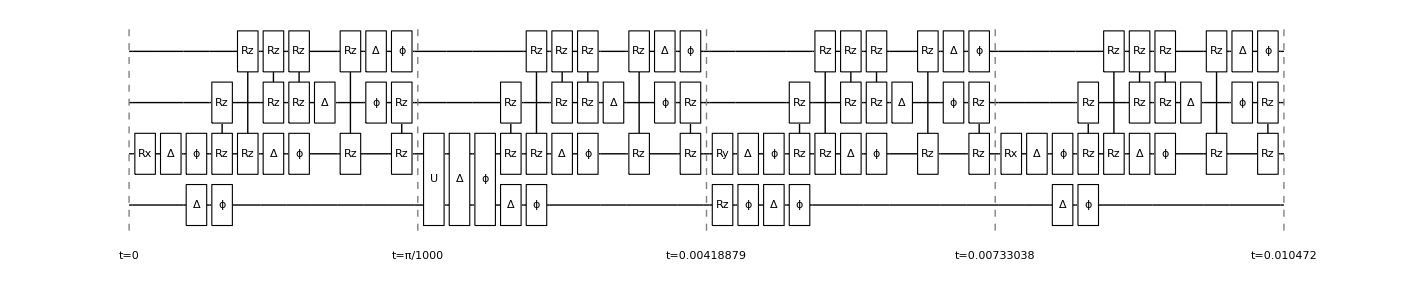

```mathematica
DrawCircuit@noisycze
```

## CZ operation between electron - nuclear spin

CZ operation between nuclear-nuclear spins uses the following tricks:
SWAP the state of nuclear spin to the electron spin , CZe, SWAP again

```mathematica
Subscript[CXen, q_/;q>0]:=Sequence @@ {Subscript[CRx, 0,q][π/2],Subscript[Rz, 0][-π/2],Subscript[Rx, q][-π/2]};
Subscript[SWAPen, q_/;q>0]:=Sequence@@{Subscript[CXen, q],Subscript[Ry, 0][-π/2],Subscript[Rz, 0][π],Subscript[Ry, q][-π/2],Subscript[Rz, q][π],Subscript[CXen, q],Subscript[Ry, 0][-π/2],Subscript[Rz, 0][π],Subscript[Ry, q][-π/2],Subscript[Rz, q][π],Subscript[CXen, q]};
Subscript[CZnn, q1_/;q1>0,q2_/;q2>0]:=Sequence@@{Subscript[SWAPen, q1],Subscript[CZen, q2],Subscript[SWAPen, q1]}
```

```mathematica
(* Check if the SWAP works *)
MatrixForm[ⅇ^(-ⅈ 3π/4)CalcCircuitMatrix@Flatten[{Subscript[SWAPen, 1]}/.NVDevice[Aliases]]]
```

(1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1)

```mathematica
(* Check if CZ between two-nuclear spins works *)
MatrixForm@ExpandAll[(ⅇ^((ⅈ π)/4)/4+ⅈ ⅇ^((-ⅈ π)/4)/4)*PartialTrace[CalcCircuitMatrix@Flatten[{Subscript[CZnn, 1,2]}/.NVDevice[Aliases]],0]]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1)

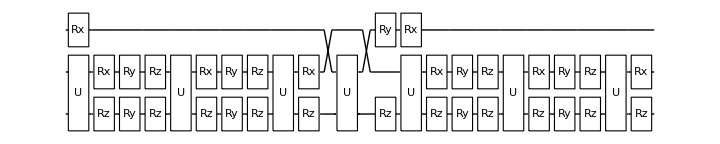

```mathematica
(* This looks overkill!!! :( *)
DrawCircuit@Flatten[{Subscript[CZnn, 1,2]}/.NVDevice[Aliases]]
```

```mathematica
noisycznn=InsertCircuitNoise[{Subscript[CZnn, 1,2]}, NVDevice,ReplaceAliases->True];
```

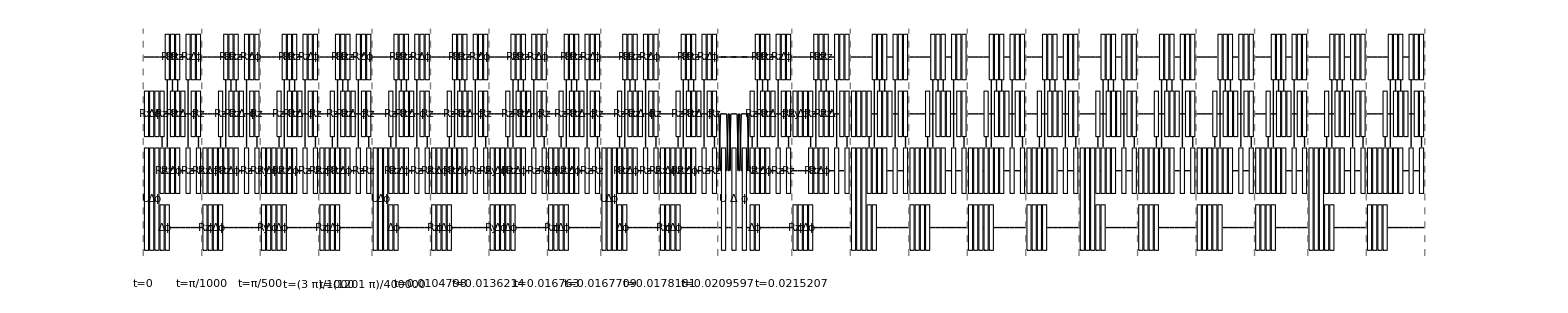

```mathematica
DrawCircuit@noisycznn
```